### plot style

```mathematica
SetOptions[{Plot, ListPlot, ListLinePlot, ListLogPlot, ListLogLogPlot}, {BaseStyle -> {FontFamily -> "Times", FontSize -> 18}, PlotStyle -> ColorData[108, "ColorList"], PlotRange -> All, Frame -> True, FrameLabel -> {"R/n^2", "E (MHz × h)"}, GridLines -> Automatic, PlotLegends -> "Expressions", ImageSize -> Medium}];
```

## two state model of f state ULRM interacting with a trilobite

## Setup

### Atomic Units Conversion

#### Boltzmann constant [T/J]

```mathematica
kB = 1.380649*10^(-23);
```

#### Bohr unit of length [m]

```mathematica
a0 = 5.29177210903*10^(-11);
```

#### time [s]

```mathematica
ts = 2.4188843265857*10^(-17);
```

#### velocity [m/s]

```mathematica
vms = 2.18769126364*10^6; (* =a0/ts *)
```

#### electron mass [kg]

```mathematica
me = 9.1093837015*10^(-31);
```

#### atomic mass in units of electron mass

```mathematica
M = 86.909180527*1822.888486192;(* atomic mass *)
```

#### temperatures from nK to K

```mathematica
T = Table[10^t, {t,-9,0,1}];
```

#### corresponding velocities in atomic units

```mathematica
vs = Sqrt[3 kB T/(M me)]/vms;
```

### Wavefunctions

#### Energies are displayed MHz

```mathematica
unit = 2 3.289841960355 10^9;
```

#### Radial hydrogenic wave function

```mathematica
U[n_,l_,r_] := Sqrt[(2/n)^3 ((n-l-1)!/(2n(n+l)!))] Exp[-r/n] (2(r/n))^l LaguerreL[n-l-1,2l+1,2(r/n)]
dU[n_,l_,r_] := D[x U[n,l,x],x] /. x->r
```

#### Radial quantum defect state wave function

```mathematica
W[n_,l_,r_] := 1/n/Sqrt[(n+l)! (n-l-1)!] WhittakerW[n,l+1/2,2r/n]/r
dW[n_,l_,r_] := D[x W[n,l,x],x] /. x->r
```

#### Angular wave function

```mathematica
Y[l_] := Sqrt[(2l+1)/(4π)]
```

#### Quantum defects for Rubidium

```mathematica
δRb = {3.1311804,2.65,1.34,0.0165192};
δ[l_]=If[l<Length[δRb],δRb[[l+1]],0];
```

#### Semi-classical electron wave number

```mathematica
kin[r_, n_] = Sqrt[2(-(2n^2)^(-1) + 1/r)];
```

#### Energy dependent scattering length (finite range theory)

```mathematica
A[k_] = -15.2+π/3 319.2Re[k];
```

#### Matrix element for the f state

```mathematica
Fstate[n_, r_] := W[n-δ[3],3,r] Y[3]
```

#### F-state energy offset

```mathematica
Fenergy[n_] := 1/2/n^2-1/2/(n-δ[3])^2
```

#### Matrix element for the trilobite

Alternative formulation for fractional n

```mathematica
TrilU[n_, r_] := Sqrt[(r(2n^2-r)(U[n,0,r]/n)^2+dU[n,0,r]^2)/(4π)]
TrilW[n_, r_] := Sqrt[(r(2n^2-r)(W[n,0,r]/n)^2+dW[n,0,r]^2)/(4π)]
Trilobite[n_, r_] := If[n∈Integers, TrilU[n,r], TrilW[n,r]]
```

However, for integer n, this is numerically more stable

```mathematica
Trilobite[n_, r_] := Sqrt[Sum[U[n,l,r]^2 Y[l]^2,{l,4,n-1}]]
```

## Electronic potentials

### Parameters

```mathematica
n0 = 99;
R = Subdivide[1.0n0^2,2.3n0^2,1000];
```

### Two state model

#### Set up 2x2 Matrix

```mathematica
Hamiltonian[n_, r_] := With[{a=2π A[kin[r,n]], t=Trilobite[n,r], f=Fstate[n,r], e=Fenergy[n]}, {{a t^2, a t f}, {a t f, e+a f^2}}]
```

#### Diagonalization

```mathematica
Diabatic = Table[Hamiltonian[n0, r], {r,R}];
Adiabatic = Table[Eigenvalues[Diabatic[[i]]], {i,Length[Diabatic]}];
```

```mathematica
dt = Diabatic[[All,1,1]];
df = Diabatic[[All,2,2]];
do = Diabatic[[All,1,2]];
at = Adiabatic[[All,1]];
af = Adiabatic[[All,2]];
```

#### Diabatic Potentials

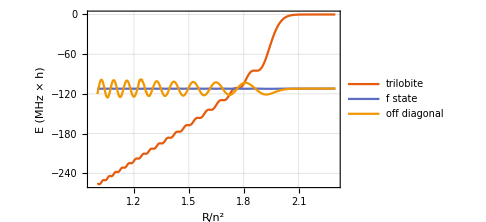

```mathematica
ListLinePlot[{{R/n0^2, dt unit}ᵀ, {R/n0^2, df unit}ᵀ, {R/n0^2, 2 do unit+df unit}ᵀ}, PlotLegends->{"trilobite", "f state", "off diagonal"}]
```

#### Adiabatic Potentials

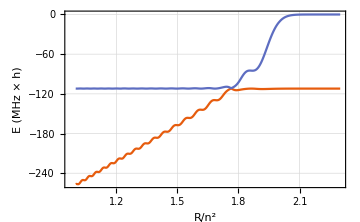

```mathematica
ListLinePlot[{{R/n0^2, at unit}ᵀ, {R/n0^2, af unit}ᵀ}]
```

## Vibrational structure

### Finite differences Hamiltonian and diagonalization

```mathematica
TridiagMat[n_,{ons_,hop_}]:=SparseArray[{Band[{1,1}]->ons,Band[{2,1}]->hop,Band[{1,2}]->hop},{n,n}]
RadSol[pot_, boundary_, gridpoints_, offset_, nstates_] := (
potINT=Interpolation[{R,pot/unit}ᵀ];
Rspan=Subdivide[R[[1]]+boundary,R[[-1]],gridpoints-1];
gridstep=N[(R[[-1]]-R[[1]]-boundary)/(gridpoints-1)];
hop=-1/(M gridstep^2);
ons=-2hop;
Ekin=TridiagMat[gridpoints,{ons,hop}];
shift=-5000IdentityMatrix[gridpoints];
H=shift+Ekin+DiagonalMatrix[potINT[Rspan]];
EigSys=Eigensystem[H,-nstates, Method->{"Arnoldi", "Shift"->offset/unit-5000}];
Vals=(Sort[EigSys[[1]]]+5000) unit;
Vecs=EigSys[[2]][[Ordering[EigSys[[1]]]]];
{Vals, Vecs, Rspan})
```

## Non-adiabatic coupling

### Vibrational states

#### Solutions for the diabatic potentials

```mathematica
VibDia1 = RadSol[dt unit,0,1001,df[[-1]] unit,100];
VibDia2 = RadSol[df unit,0,1001,df[[-1]] unit,100];
```

#### Vibrational states in the trilobite potential

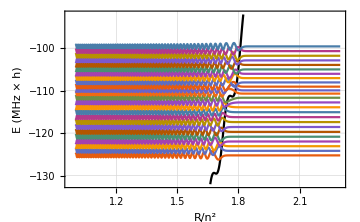

```mathematica
Show[ListLinePlot[{R/n0^2,dt unit}ᵀ, PlotStyle->Black, PlotRange->{df[[-1]] unit-20,df[[-1]] unit+20}],
ListLinePlot[Evaluate@Table[{VibDia1[[3]]/n0^2,VibDia1[[1,i]]+10VibDia1[[2,i]]}ᵀ, {i,37,61}]]]
```

#### Vibrational states in the f-state potential

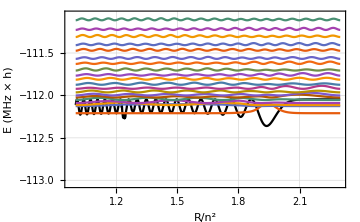

```mathematica
Show[ListLinePlot[{R/n0^2,df unit}ᵀ, PlotStyle->Black, PlotRange->{df[[-1]] unit-1,df[[-1]] unit+1}],
ListLinePlot[Evaluate@Table[{VibDia1[[3]]/n0^2,VibDia2[[1,i]]+10VibDia2[[2,i]]^2}ᵀ, {i,20}]]]
```

#### Solutions for the adiabatic potentials

```mathematica
VibAdia1 = RadSol[at unit,0,1001,df[[-1]] unit,100];
VibAdia2 = RadSol[af unit,0,1001,df[[-1]] unit,100];
```

#### Vibrational states in the trilobite potential

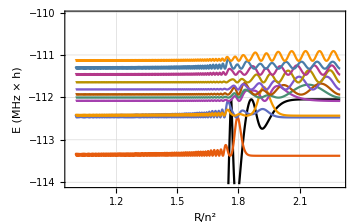

```mathematica
Show[ListLinePlot[{R/n0^2,at unit}ᵀ, PlotStyle->Black, PlotRange->{df[[-1]] unit-2,df[[-1]] unit+2}],
ListLinePlot[Evaluate@Table[{VibAdia1[[3]]/n0^2,VibAdia1[[1,i]]+50VibAdia1[[2,i]]^2}ᵀ, {i,30,40}]]]
```

#### Vibrational states in the f-state potential

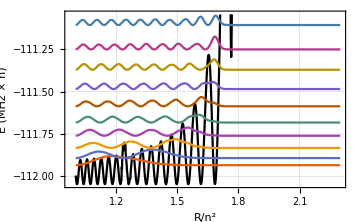

```mathematica
Show[ListLinePlot[{R/n0^2,af unit}ᵀ, PlotStyle->Black, PlotRange->{df[[-1]] unit,df[[-1]] unit+1}],
ListLinePlot[Evaluate@Table[{VibAdia1[[3]]/n0^2,VibAdia2[[1,i]]+10VibAdia2[[2,i]]^2}ᵀ, {i,20}]]]
```

### Effective Hamiltonian

#### Setup

```mathematica
doINT=Interpolation[{R,do unit}ᵀ];
EHon1 = DiagonalMatrix[VibDia1[[1]]];
EHon2 = DiagonalMatrix[VibDia2[[1]]];
EHoff = Table[Total[VibDia1[[2, i]] VibDia2[[2, j]] doINT[VibDia1[[3]]]], {i, 100}, {j, 100}];
EH = ArrayFlatten[{{EHon1, EHoff}, {EHoffᵀ, EHon2}}];
```

#### Diagonalize

```mathematica
{Eν, Cν} = Eigensystem[EH];
Vib = Cν.Join[VibDia1[[2]],VibDia2[[2]]];
```

#### Plot

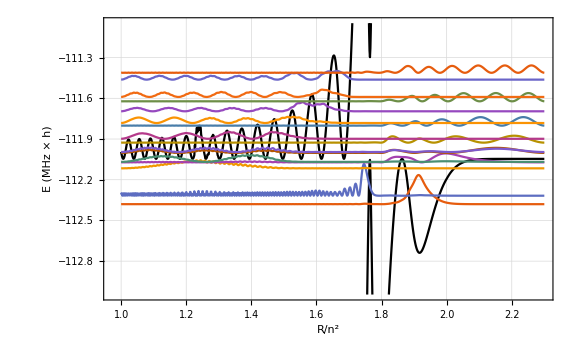

```mathematica
Show[ListLinePlot[{{R/n0^2,at unit}ᵀ,{R/n0^2,af unit}ᵀ}, PlotStyle->Black, PlotRange->{df[[-1]] unit-1,df[[-1]] unit+1}],
ListLinePlot[Evaluate@Table[{VibDia1[[3]]/n0^2,Eν[[i]]+10Vib[[i]]^2}ᵀ, {i,50,65}]], ImageSize -> Large]
```

#### mixing of states

```mathematica
ArrayPlot[Cν, PlotLegends->True]
```

-Graphics-

#### off diagonal elements

```mathematica
MatrixPlot[EHoff, PlotLegends->True]
```

-Graphics-

### Dynamics

#### Initial wave packet

Let’s start with a box state above the diabatic f-state

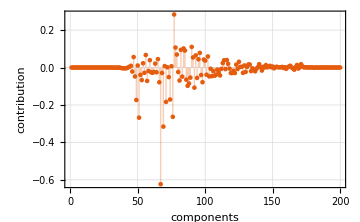

```mathematica
CI=Cν[[All,50]];
ListPlot[{CI}, Filling->Axis, FrameLabel->{"components", "contribution"}]
```

In the basis of the diabatic potentials the state looks like this

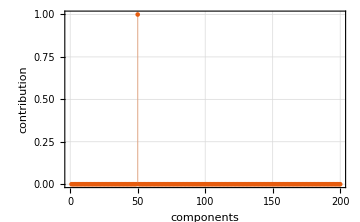

```mathematica
ListPlot[{Cνᵀ.CI}, Filling->Axis, FrameLabel->{"components", "contribution"}]
```

This is the spacial representation

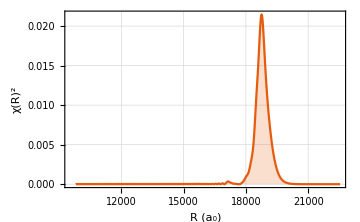

```mathematica
ψI=Cνᵀ.CI.Vib;
ListLinePlot[{ψI^2}, DataRange->{R[[1]],R[[-1]]}, FrameLabel->{"R (a_0)", "χ(R)^2"}, Filling->Axis]
```

#### Autocorrelation function

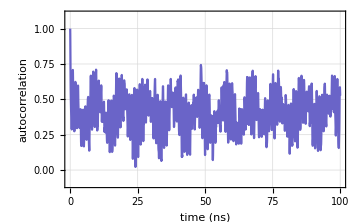

```mathematica
autocorr[t_] := CI.(Exp[-2π I t Eν]*CI)
Plot[Abs[autocorr[t]], {t,0,100}, FrameLabel -> {"time (ns)", "autocorrelation"}, PlotRange->{-0.1,1.1}]
```

#### Time propagation of participating states

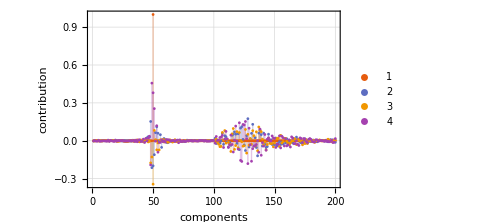

```mathematica
ψ[t_] := Cνᵀ.(Exp[-2π I t Eν]*CI)
ListPlot[Table[Re[ψ[i]],{i,0,30,10}], Filling->Axis, PlotLegends->Automatic, FrameLabel->{"components", "contribution"}]
```

#### Spacial representation

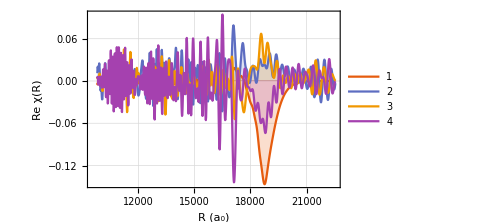

```mathematica
ListLinePlot[Table[Re[ψ[i]].Vib,{i,0,30,10}], DataRange->{R[[1]],R[[-1]]}, FrameLabel->{"R (a_0)", "Re χ(R)"}, Filling->Axis, PlotLegends->Automatic]
```

#### Participating states

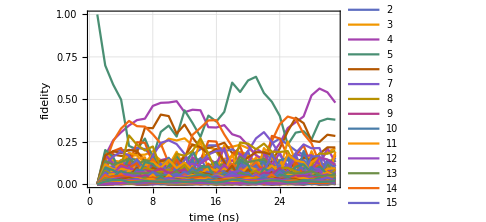

```mathematica
StateFidelity=Table[Abs[ψ[t]], {t,0,30,1}];
ListLinePlot[StateFidelityᵀ, FrameLabel->{"time (ns)", "fidelity"},PlotLegends->Automatic, PlotRange->All]
```

#### Damping functions

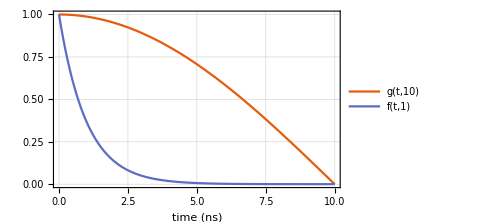

```mathematica
g[t_,τ_] = If[1-Abs[t]/τ≠0, Cos[π*t/τ/2]*HeavisideTheta[1-Abs[t]/τ], 0];
f[t_, τ_] = Exp[-t/τ];
Plot[{g[t,10], f[t,1]}, {t,0,10}, FrameLabel -> "time (ns)"]
```

#### Naive spectrum

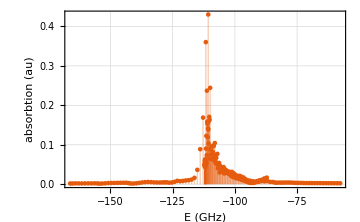

```mathematica
ListPlot[{{Diagonal[EH], Total[StateFidelity]/30}ᵀ}, Filling -> Axis, FrameLabel -> {"E (GHz)", "absorbtion (au)"}]
```

#### Absorption spectrum

```mathematica
num = 2^9; (*sample points*)
TT = 1000; (*sampling time in ns*)
dτ = N[TT/num]; (*step size in time domain*)
dω = N[1/TT]; (*step size in frequency domain*)
time = Range[num]*dτ;
freq = Range[num]*dω;
AC = Table[autocorr[t]*f[t, TT/10], {t, 0, TT - 1, dτ}];
```

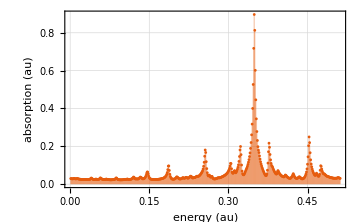

```mathematica
AS = Fourier[AC];
ListPlot[{{freq,Abs[AS]}ᵀ}, FrameLabel->{"energy (au)", "absorption (au)"}, Filling->Axis]
```

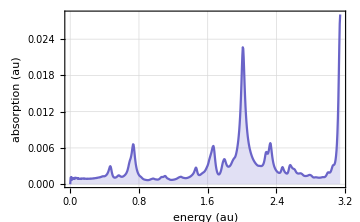

```mathematica
Plot[Abs[PowerSpectralDensity[AC,ω]],{ω,0,π}, FrameLabel->{"energy (au)", "absorption (au)"}, PlotPoints->10, Filling->Axis, PlotRange->All]
```